\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Introduction to Mathematica (MMA) -- 01

Zu-Cheng Chen

Institute of Theoretical Physics, 
Chinese Academy of Sciences

@ Guangzhou University, Jul 2019

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Overview of Mathematica (MMA)

## Easy to learn/use

Many predefined functions.
Press Shift+Enter to evaluate cells.

```mathematica
Print["Hello, World!"]
```

Hello, World!

## Functional programming

More than 4000 predefined functions!

```mathematica
TrigExpand[Sin[ArcSin[t]+ArcSin[v]]]
```

√(1-t^2) v+t √(1-v^2)

## Dynamical language

Define a function.

```mathematica
f[x_]:=x^2
f[2]
```

4

No need to declare types of variables.
Redefine variable dynamically.

```mathematica
f=.
f[x_]:=x^3
f[2]
```

8

```mathematica
f = 3
```

3

```mathematica
f[2.0]
```

8.

```mathematica
f["hi"]
```

hi^3

## Symbolic calculation

```mathematica
∫_0^1 (∑_(k=1)^∞ x^k/k^2)ⅆx
∑_(k=1)^∞ ∫_0^1 x^k/k^2 ⅆx
```

1/6 (-6+π^2)

1/6 (-6+π^2)

```mathematica
∫x Sin[x^2]ⅆx
```

-1/2 Cos[x^2]

```mathematica
Integrate[x*Sin[x^2],x]
```

-1/2 Cos[x^2]

```mathematica
∫_-1^3 x Sin[x^2]ⅆx
```

1/2 (Cos[1]-Cos[9])

```mathematica
Integrate[x*Sin[x^2],{x,-1,3}]//N
```

0.725716

## Numeric calculation

```mathematica
NIntegrate[x*Sin[x^2],{x,-1,3}]
```

0.725716

```mathematica
N[π,10001]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491298336733624406566430860213949463952247371907021798609437027705392171762931767523846748184676694051320005681271452635608277857713427577896091736371787214684409012249534301465495853710507922796892589235420199561121290219608640344181598136297747713099605187072113499999983729780499510597317328160963185950244594553469083026425223082533446850352619311881710100031378387528865875332083814206171776691473035982534904287554687311595628638823537875937519577818577805321712268066130019278766111959092164201989380952572010654858632788659361533818279682303019520353018529689957736225994138912497217752834791315155748572424541506959508295331168617278558890750983817546374649393192550604009277016711390098488240128583616035637076601047101819429555961989467678374494482553797747268471040475346462080466842590694912933136770289891521047521620569660240580381501935112533824300355876402474964732639141992726042699227967823547816360093417216412199245863150302861829745557067498385054945885869269956909272107975093029553211653449872027559602364806654991198818347977535663698074265425278625518184175746728909777727938000816470600161452491921732172147723501414419735685481613611573525521334757418494684385233239073941433345477624168625189835694855620992192221842725502542568876717904946016534668049886272327917860857843838279679766814541009538837863609506800642251252051173929848960841284886269456042419652850222106611863067442786220391949450471237137869609563643719172874677646575739624138908658326459958133904780275900994657640789512694683983525957098258226205224894077267194782684826014769909026401363944374553050682034962524517493996514314298091906592509372216964615157098583874105978859597729754989301617539284681382686838689427741559918559252459539594310499725246808459872736446958486538367362226260991246080512438843904512441365497627807977156914359977001296160894416948685558484063534220722258284886481584560285060168427394522674676788952521385225499546667278239864565961163548862305774564980355936345681743241125150760694794510965960940252288797108931456691368672287489405601015033086179286809208747609178249385890097149096759852613655497818931297848216829989487226588048575640142704775551323796414515237462343645428584447952658678210511413547357395231134271661021359695362314429524849371871101457654035902799344037420073105785390621983874478084784896833214457138687519435064302184531910484810053706146806749192781911979399520614196634287544406437451237181921799983910159195618146751426912397489409071864942319615679452080951465502252316038819301420937621378559566389377870830390697920773467221825625996615014215030680384477345492026054146659252014974428507325186660021324340881907104863317346496514539057962685610055081066587969981635747363840525714591028970641401109712062804390397595156771577004203378699360072305587631763594218731251471205329281918261861258673215791984148488291644706095752706957220917567116722910981690915280173506712748583222871835209353965725121083579151369882091444210067510334671103141267111369908658516398315019701651511685171437657618351556508849099898599823873455283316355076479185358932261854896321329330898570642046752590709154814165498594616371802709819943099244889575712828905923233260972997120844335732654893823911932597463667305836041428138830320382490375898524374417029132765618093773444030707469211201913020330380197621101100449293215160842444859637669838952286847831235526582131449576857262433441893039686426243410773226978028073189154411010446823252716201052652272111660396665573092547110557853763466820653109896526918620564769312570586356620185581007293606598764861179104533488503461136576867532494416680396265797877185560845529654126654085306143444318586769751456614068007002378776591344017127494704205622305389945613140711270004078547332699390814546646458807972708266830634328587856983052358089330657574067954571637752542021149557615814002501262285941302164715509792592309907965473761255176567513575178296664547791745011299614890304639947132962107340437518957359614589019389713111790429782856475032031986915140287080859904801094121472213179476477726224142548545403321571853061422881375850430633217518297986622371721591607716692547487389866549494501146540628433663937900397692656721463853067360965712091807638327166416274888800786925602902284721040317211860820419000422966171196377921337575114959501566049631862947265473642523081770367515906735023507283540567040386743513622224771589150495309844489333096340878076932599397805419341447377441842631298608099888687413260472156951623965864573021631598193195167353812974167729478672422924654366800980676928238280689964004824354037014163149658979409243237896907069779422362508221688957383798623001593776471651228935786015881617557829735233446042815126272037343146531977774160319906655418763979293344195215413418994854447345673831624993419131814809277771038638773431772075456545322077709212019051660962804909263601975988281613323166636528619326686336062735676303544776280350450777235547105859548702790814356240145171806246436267945612753181340783303362542327839449753824372058353114771199260638133467768796959703098339130771098704085913374641442822772634659470474587847787201927715280731767907707157213444730605700733492436931138350493163128404251219256517980694113528013147013047816437885185290928545201165839341965621349143415956258658655705526904965209858033850722426482939728584783163057777560688876446248246857926039535277348030480290058760758251047470916439613626760449256274204208320856611906254543372131535958450687724602901618766795240616342522577195429162991930645537799140373404328752628889639958794757291746426357455254079091451357111369410911939325191076020825202618798531887705842972591677813149699009019211697173727847684726860849003377024242916513005005168323364350389517029893922334517220138128069650117844087451960121228599371623130171144484640903890644954440061986907548516026327505298349187407866808818338510228334508504860825039302133219715518430635455007668282949304137765527939751754613953984683393638304746119966538581538420568533862186725233402830871123282789212507712629463229563989898935821167456270102183564622013496715188190973038119800497340723961036854066431939509790190699639552453005450580685501956730229219139339185680344903982059551002263535361920419947455385938102343955449597783779023742161727111723643435439478221818528624085140066604433258885698670543154706965747458550332323342107301545940516553790686627333799585115625784322988273723198987571415957811196358330059408730681216028764962867446047746491599505497374256269010490377819868359381465741268049256487985561453723478673303904688383436346553794986419270563872931748723320837601123029911367938627089438799362016295154133714248928307220126901475466847653576164773794675200490757155527819653621323926406160136358155907422020203187277605277219005561484255518792530343513984425322341576233610642506390497500865627109535919465897514131034822769306247435363256916078154781811528436679570611086153315044521274739245449454236828860613408414863776700961207151249140430272538607648236341433462351897576645216413767969031495019108575984423919862916421939949072362346468441173940326591840443780513338945257423995082965912285085558215725031071257012668302402929525220118726767562204154205161841634847565169998116141010029960783869092916030288400269104140792886215078424516709087000699282120660418371806535567252532567532861291042487761825829765157959847035622262934860034158722980534989650226291748788202734209222245339856264766914905562842503912757710284027998066365825488926488025456610172967026640765590429099456815065265305371829412703369313785178609040708667114965583434347693385781711386455873678123014587687126603489139095620099393610310291616152881384379099042317473363948045759314931405297634757481193567091101377517210080315590248530906692037671922033229094334676851422144773793937517034436619910403375111735471918550464490263655128162288244625759163330391072253837421821408835086573917715096828874782656995995744906617583441375223970968340800535598491754173818839994469748676265516582765848358845314277568790029095170283529716344562129640435231176006651012412006597558512761785838292041974844236080071930457618932349229279650198751872127267507981255470958904556357921221033346697499235630254947802490114195212382815309114079073860251522742995818072471625916685451333123948049470791191532673430282441860414263639548000448002670496248201792896476697583183271314251702969234889627668440323260927524960357996469256504936818360900323809293459588970695365349406034021665443755890045632882250545255640564482465151875471196218443965825337543885690941130315095261793780029741207665147939425902989695946995565761218656196733786236256125216320862869222103274889218654364802296780705765615144632046927906821207388377814233562823608963208068222468012248261177185896381409183903673672220888321513755600372798394004152970028783076670944474560134556417254370906979396122571429894671543578468788614445812314593571984922528471605049221242470141214780573455105008019086996033027634787081081754501193071412233908663938339529425786905076431006383519834389341596131854347546495569781038293097164651438407007073604112373599843452251610507027056235266012764848308407611830130527932054274628654036036745328651057065874882256981579367897669742205750596834408697350201410206723585020072452256326513410559240190274216248439140359989535394590944070469120914093870012645600162374288021092764579310657922955249887275846101264836999892256959688159205600101655256375679

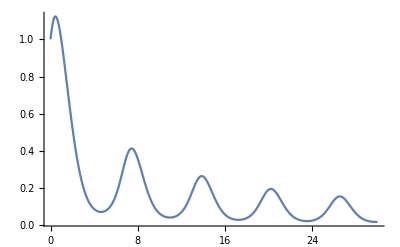

```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}];
Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]
```

## Visualization

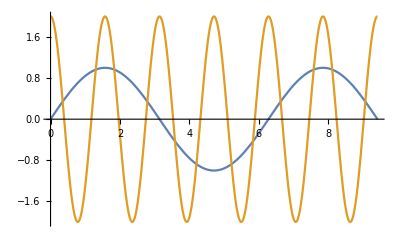

```mathematica
Plot[{Sin[x],2*Cos[4*x]},{x,0,3*π}]
```

```mathematica
Plot3D[Sin[x+Cos[y]],{x,0,4*π},{y,0,4*π},Boxed->False,Axes->None]
```

-Graphics3D-

## Slow to run, but fast to write.

Suppose 

 C : 1000 lines; 1 day to write; 1 minute to run; 
MMA : 50 lines; 1 hour to write; 1 hour to run; 

Will you choose C or MMA ?

## Property software: not open, neither free

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

## Be familiar with notebook

## Cells

Input cell;
Output cell;
Cell groups;

```mathematica
Print["Hello, World!"]
```

Hello, World!

## Help system: F1 ? ??

```mathematica
Integrate[BesselJ[n,x],x]
```

2^(-1-n) x^(1+n) Gamma[(1+n)/2] HypergeometricPFQRegularized[{(1+n)/2},{1+n,(3+n)/2},-x^2/4]

```mathematica
?BesselJ
```

```mathematica
??BesselJ
```

## Suppress outputs ( ; )

```mathematica
1+1
```

2

```mathematica
1+1;
```

```mathematica
a=2
```

2

```mathematica
Out[40]
```

%40

## Last output: % Last last output: %%

```mathematica
1+1
%
```

2

2

```mathematica
a=3;
b=4;
%%
```

3

```mathematica
%%%
```

3

## Timing AbsoluteTiming

```mathematica
Clear[x];
Integrate[Sin[x],x]//Timing
```

{0.004339,-Cos[x]}

```mathematica
Integrate[Sin[x],x]//Timing
```

{0.003615,-Cos[x]}

```mathematica
Integrate[Sin[x],x]//AbsoluteTiming
```

{0.003283,-Cos[x]}

## Shortcut keys see: tutorial/KeyboardShortcutListing

### Abort an evaluation: Alt+. Evaluation->Quit Kernel->Local

```mathematica
f[x_]:=(Sin[x]/x^4-Cos[x]/x^3)^100;
Timing[∫f[x]ⅆx;]
```

$Aborted

### Fullscreen: F12

### Styles: Format->Style

Alt+1: Title
Alt+2: Chapter
...
Alt+6: Subsubsection
...

### Comments: Alt+/

```mathematica
(*This is a comment*)
```

```mathematica
(*f[x] gives the square of x.*)
f[x_]:=x^2

(*x=2
f[x]*)
```

## Better format

```mathematica
Pi
```

π

```mathematica
(*Esc+pi+Esc*)
Pi==π
```

True

```mathematica
π==a
```

True

```mathematica
(*x;ctrl+^;2*)
x^2==x^2
```

True

```mathematica
(*Ctrl+-*)
Subscript[A, i]
```

A_i

```mathematica
(*ctrl+2;3*)
Sqrt[3]==√3
```

True

```mathematica
x=.
x^2/(x+1)
```

x^2/(1+x)

```mathematica
(*Ctrl+/*)
x^2/(x+1)
```

x^2/(1+x)

## Clear/Remove variables

```mathematica
?f
```

### Clear

```mathematica
Clear[f]
?f
```

```mathematica
a=3
?a
```

3

```mathematica
Clear[a]
```

### Unset (.)

```mathematica
a=3
```

3

```mathematica
a=.
?a
```

### Remove

```mathematica
a=3
Remove[a]
```

3

```mathematica
?a
```

Missing[UnknownSymbol,a]

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Function -- part 1

## Define a function: f[x_]:=a*x+b

```mathematica
a=3;
b=2;
```

### Correct way

```mathematica
Clear[f]
f[x_]:=a*x+b
?f
```

```mathematica
f[3]
```

11

### Wrong way 1: f[x]:=a*x+b

```mathematica
Clear[f]
x=.
f[x]:=a*x+b
?f
```

```mathematica
f[3]
```

f[3]

```mathematica
f[x]
```

1+3 x

```mathematica
f[y]
```

f[y]

### (Not totally) wrong way 2: f[x_]=a*x+b Be careful if you use this definition!

```mathematica
Clear[f]
f[x_]=a*x+b
?f
```

1+3 x

```mathematica
f[3]
```

10

```mathematica
x=5;
```

```mathematica
Clear[f]
f[x_]=a*x+b
?f
```

16

```mathematica
f[3]
```

16

```mathematica
f[x]
```

16

```mathematica
f[4]
```

16

### Wrong way 3: f[x]=a*x+b

```mathematica
x=5;
```

```mathematica
Clear[f]
f[x]=a*x+b
?f
```

16

```mathematica
f[3]
```

f[3]

```mathematica
x=.
f[x]
```

f[x]

```mathematica
f[4]
```

f[4]

## Pattern

```mathematica
Clear[g,f,x]
g[x]=x+1; 
f[x_]=x+1;
```

```mathematica
{g[x],f[x]}
```

{1+x,1+x}

```mathematica
{g[y],f[y]}
```

{g[y],1+y}

```mathematica
x=2;
{g[x],f[x]}
```

{g[2],3}

### Exercise

What is the result of f[3] if function f is defined as:
x = 2; 
f[x_] = x + 1;

```mathematica
x = 2; 
f[x_] = x + 1;
```

```mathematica
f[3]
```

3

## Set(=) and SetDelayed(:=)

```mathematica
x=1;
a = x+1;
b:=x+1;
```

```mathematica
{a,b}
```

{2,2}

```mathematica
x=2;
{a,b}
```

{2,3}

```mathematica
?a
```

```mathematica
?b
```

### Exercise

```mathematica
RandomReal[ ]
```

0.198478

```mathematica
c = RandomReal[ ]; 
d := RandomReal [ ];
```

Will following expressions all equals to 0?
Can you explain why?
c - c
c - d
d - d

```mathematica
c-c
```

0.

```mathematica
c-d
```

0.0816242

```mathematica
d-d
```

-0.433657

```mathematica
d
```

0.145791

```mathematica
d
```

0.728284

```mathematica
d-d
```

-0.292523

## Call a function (f[x_]:=x^2): f[2] f@2 2//f

```mathematica
f[x_]:=x^2
```

```mathematica
f[2]
```

4

```mathematica
f@2
```

4

```mathematica
2//f
```

4

```mathematica
π//N//Cos//Sin
```

-0.841471

```mathematica
Sin[Cos[N[π]]]
```

-0.841471

```mathematica
f[x_,y_]:=x+y
```

```mathematica
f[2,3]
```

5

```mathematica
2~f~3
```

5

## Piecewise function

g(x)=Piecewise[{{x,, 0≤x<1}, {1,, 1≤x<2}, {3-x,, 2≤x<3}, {g(x-3),, x≥3}}]

Method 1

```mathematica
g1[x_]:=x/;0≤x<1
g1[x_]:=1/;1≤x<2
g1[x_]:=3-x/;2≤x<3
g1[x_]:=g1[x-3]/;x≥3
```

```mathematica
?g1
```

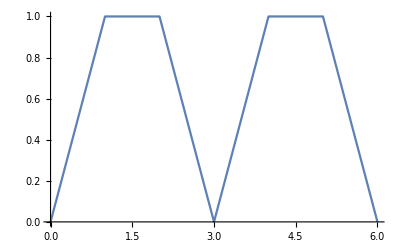

```mathematica
Plot[g1[x],{x,0,6}]
```

Method 2

```mathematica
g2[x_]:=Piecewise[{
{x, 0≤x<1},
{1, 1≤x<2},
{3-x, 2≤x<3},
{g2[x-3], x≥3}
}]
```

```mathematica
Plot[g2[x],{x,0,6}]
```

-Graphics-

### Exercise

Plot function 
f(x)=Piecewise[{{x^2,, x<0}, {x,, x>0}}]
for x in the range (-5, 5).

```mathematica
f=.
f[x_]:=Piecewise[{
{x^2,x<0},
{x,x>0}
}]
```

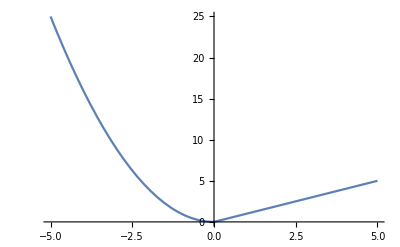

```mathematica
Plot[f[x],{x,-5,5}]
```

## An example: Fibonacci Sequence

1, 1, 2, 3, 5, 8, 13, 21, 34, ...
F_n = F_(n-1) + F_(n-2)
F_1=F_2=1

Question: what is F_20 and F_40?

### Original version

```mathematica
?F
```

```mathematica
F[1]=1;
F[2]=1;
F[n_]:=F[n-1]+F[n-2]
```

```mathematica
F[32]//AbsoluteTiming
```

{3.13247,2178309}

### Improved version

```mathematica
Clear@F
F[1]=1;
F[2]=1;
F[n_]:=F[n]=F[n-1]+F[n-2]
```

```mathematica
F[10]//AbsoluteTiming
```

{0.000068,55}

```mathematica
?F
```

## Name your functions

* Case sensitive
* User defined function should start with lower case letter
myFunction
* System functions always start with capital letter
* A function’s name should be meaningful

```mathematica
Sin[1.]
```

0.841471

\[FirstPage] | ◂ | ▸ | \[LastPage] |   | SlideShowNavigationBar of SlideShowNavigationBar

Predefined functions

## Integrate

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
Integrate[1/(x^3+1),{x,1,2.0}]
```

0.254353

## D==Derivative==’

```mathematica
x=.
D[Sin[x],x]
Sin'[x]
```

Cos[x]

Cos[x]

```mathematica
D[Integrate[1/(x^3+1),x],x]
```

1/(3 (1+x))-(-1+2 x)/(6 (1-x+x^2))+2/(3 (1+1/3 (-1+2 x)^2))

## Simplify

```mathematica
Cos[x]^2+Sin[x]^2//Simplify
```

1

```mathematica
Simplify[Cos[x]^2+Sin[x]^2]
```

1

```mathematica
D[Integrate[1/(x^3+1),x],x]//Simplify
```

1/(1+x^3)

## FullSimplify

```mathematica
Simplify[Cosh[x]-Sinh[x]]
```

Cosh[x]-Sinh[x]

```mathematica
FullSimplify[Cosh[x]-Sinh[x]]
```

ⅇ^-x

## TrigToExp

```mathematica
Cosh[x]-Sinh[x]//TrigToExp
```

ⅇ^-x

## Log

```mathematica
E//N
```

2.71828

```mathematica
Log[E]
```

1

```mathematica
Log10[10]
```

1

## Factor

```mathematica
12*x^2+27*x*y-84*y^2
%//Factor
```

12 x^2+27 x y-84 y^2

3 (4 x-7 y) (x+4 y)

## Expand

```mathematica
Expand[-6 (1+2 y) (-8+7 y)]
```

48+54 y-84 y^2

## Together

```mathematica
2/x^2-x^2/2//Together
```

(4-x^4)/(2 x^2)

## Apart

```mathematica
1/((x-3)*(x-1))//Apart
```

1/(2 (-3+x))-1/(2 (-1+x))

## Cancel

```mathematica
(x^2-1)/(x^2-2*x+1)//Cancel
```

(1+x)/(-1+x)

## PowerExpand

```mathematica
a=.
b=.
√(a^2*b^4)
%//PowerExpand
```

√(a^2 b^4)

a b^2

## Solve

```mathematica
Solve[3*x+7==4]
```

{{x→-1}}

## Series

```mathematica
Series[Cos[xx]/xx,{xx,0,5}]//Normal
```

1/xx-xx/2+xx^3/24-xx^5/720

## Limit

```mathematica
Limit[Sin[xx]/xx,xx->0]
```

1

## TrigReduce

```mathematica
Sin[3*x]*Cos[5*x]//TrigReduce
```

1/2 (-Sin[2 x]+Sin[8 x])

## TrigExpand

```mathematica
Sin[3*x]*Cos[5*x]//TrigExpand
```

-Cos[x] Sin[x]+4 Cos[x]^7 Sin[x]-28 Cos[x]^5 Sin[x]^3+28 Cos[x]^3 Sin[x]^5-4 Cos[x] Sin[x]^7

## NSolve

```mathematica
f[x_]:=x^5-2*x+3
```

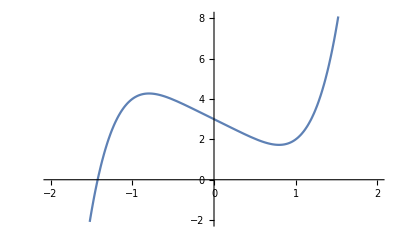

```mathematica
Plot[f[x],{x,-2,2}]
```

```mathematica
NSolve[f[x]==0,x]
```

{{x→-1.42361},{x→-0.246729-1.32082 ⅈ},{x→-0.246729+1.32082 ⅈ},{x→0.958532-0.498428 ⅈ},{x→0.958532+0.498428 ⅈ}}

```mathematica
NSolve[f[x]==0,x,Reals]
```

{{x→-1.42361}}

## FindRoot

```mathematica
f[x_]:=E^x-x^2+3
```

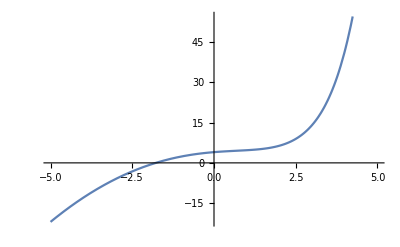

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
NSolve[f[x]==0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[3+ⅇ^x-x^2==0,x]

```mathematica
FindRoot[f[x]==0,{x,0}]
```

{x→-1.78006}